## Bethe Ansatz for the Heisenberg XX Chain

```mathematica
Quit
```

### Part 1) Define the Hamiltonian in Mathematica.

#### The Hamiltonian is

```mathematica
H == -1/2∑_(i=1)^L (Subscript[σ̄, i].Subscript[σ̄, i+1]-IdentityMatrix[2^L]);
```

#### In Mathematica syntax, we define the intermediate objects

```mathematica
tensorPower[tensor_?MatrixQ,n_?IntegerQ]:= If[
n>0,
Nest[KroneckerProduct[#,tensor]&,
tensor,n-1],
{1}]
```

```mathematica
Subscript[σ, nn_,j_]:=Module[{part1, part1size,part3,part3size,n},
n = Mod[nn,L,1];
part1size = n-1;
part3size = L-n;
part1= tensorPower[IdentityMatrix[2],part1size];
part3 = tensorPower[IdentityMatrix[2],part3size];
KroneckerProduct[part1, PauliMatrix[Mod[j,3,1]], part3]
]
```

How to take powers of dot products of vectors with matrix entries like ?

```mathematica
vecMatDot[vec1_,vec2_]:= Module[{dim},
dim = Min[Length@vec1,Length@vec2];
Sum[vec1[[j]].vec2[[j]],{j,1,dim}]
]
```

```mathematica
Subscript[vecσ, n_]:= Table[Subscript[σ, n,j],{j,1,3}];
```

```mathematica
Subscript[dotσ2, n_]:=vecMatDot[Subscript[vecσ, n],Subscript[vecσ, n+1]]
```

```mathematica
Subscript[dotσ, n_]:=Sum[Subscript[σ, n,j].Subscript[σ, n+1,j],{j,1,3}];
```

```mathematica
L=5;
```

```mathematica
Table[Subscript[dotσ, n]==Subscript[dotσ2, n],{n,1,L}]
```

{True,True,True,True,True}

#### and finally the Hamiltonian

```mathematica
H[l_?IntegerQ]:=H[l]= Module[{ham},
LL=L;
Clear[L];
L=l;
ham= -1/2(Sum[Subscript[dotσ, i]-IdentityMatrix[2^l],{i,1,l}]);
Clear[L];
L=LL;
Clear[LL];
ham]
```

```mathematica
L=2;
Subscript[dotσ, 2]
```

{{1,0,0,0},{0,-1,2,0},{0,2,-1,0},{0,0,0,1}}

```mathematica
H[4]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 2 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 2 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 4 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 2 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0
0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 4 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 2 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 2 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Table[H[i]==H[i]†, {i,1,8}]
```

{True,True,True,True,True,True,True,True}

### Part 2) Define the basis states

#### The up and down states, we will represent in the computational basis

```mathematica
up= {1,0};
down={0,1};
```

#### We need to take the trace of an array of spins, where the trace uses the tensor product instead of a sum :

```mathematica
tensorTrace[arr_?ArrayQ,op_]:= Module[{i,trace},
trace =Join[{arr[[1]]},Array[Identity[{0,0}]&, {Length@arr-1}]];
For[i=1, i<Length@arr,i++,
trace[[i+1]] = Flatten@(op[trace[[i]],arr[[i+1]]]) ;
];
trace[[-1]]]
```

#### We represent a state with nn_ down spins at coordinates given by an array pos_, and the total number of spins is dim:

```mathematica
Subscript[nn_?IntegerQ,pos_?VectorQ, dim_?IntegerQ]:= Module[{n,i},
Catch[
If[
Or[nn>dim, Length@pos>dim],
Throw["Number of down spins or length of position array larger than chain length."],
If[nn>dim,n=dim,n=nn]; 

state = Array[0, {dim}];
For[i=1, i<=dim,i++,
state[[i]]=If[MemberQ[pos, i],down,up ]
];
Return[tensorTrace[state,TensorProduct]];
]
]]
```

#### Examples:

The state with all spins up, where we have 4 spins in total:

```mathematica
Subscript[0,{}, 4]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

A state with 1 down spin out of 4 total spins, at position 1 :

```mathematica
Subscript[1,{1}, 4]
```

{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}

A state with 3 down spins out of 4 total spins, at positions 0,1,4 :

```mathematica
Subscript[3,{1,2,4}, 4]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0}

#### Does it work for larger spin chains?

```mathematica
Subscript[3,{1,2,4}, 6]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}

#### Now the 0 down particle state is (given L = 4 as example)

```mathematica
Subscript[0, 4]=Subscript[0,{}, 4]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Subscript[0, n_]:=Subscript[0,{}, n]
```

```mathematica
x0 = 0
x1 = 1
x2 = 2,3,4
3
x1 = 2
x2 = 3,4
2
x1 = 3
x2 = 4
1
x0 = 1 
x1 = 2
x2 = 3,4
2
x1=3
x2=4
1
x0=2
x1=3
x2=4
1
x0=3
x1 = 4
x2
```

0

1

#### Check if ground state is annihilated (by utilizing that trace of {0,0,0, ..., 0} is 0):

```mathematica
Table[Tr[H[i].Subscript[0, i]],{i,2,8}]
```

{0,0,0,0,0,0,0}

### Part 3) Show that the 1-particle state is an eigenstate of H.

The 1 - particle state is a superposition of the 1 - spin down states at each possible position, weighted by its momentum :

```mathematica
Subscript[ψ[k_], L_]:= Sum[Exp[ⅈ k x]*Subscript[1,{x}, L],{x,1,L}]
```

```mathematica
ϵ[k_]:= 4 Sin[k/2]^2
```

```mathematica
Solve[H[4].Subscript[ψ[k], 4]==ϵ[k] Subscript[ψ[k], 4],k]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→0},{k→-π/2},{k→π/2},{k→π}}

```mathematica
Solve[Exp[ⅈ k 4]== 1,k]
```

{{k→ConditionalExpression[(π C[1])/2, C[1]∈ℤ]}}

```mathematica
Solve[H[6].Subscript[ψ[k], 6]==ϵ[k] Subscript[ψ[k], 6],k]
Solve[Exp[ⅈ k 6]== 1,k]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→0},{k→-(2 π)/3},{k→-π/3},{k→π/3},{k→(2 π)/3},{k→π}}

{{k→ConditionalExpression[(π C[1])/3, C[1]∈ℤ]}}

The 1 - particle state is an eigenstate if the quantization condition holds, e^(i k L)=1.

### Part 4) Time evolution of spin dispersion.

The state that the m^th spin is down:

```mathematica
Subscript[Subscript[ψ, m_], L_] := Subscript[1,{m}, L]
```

```mathematica
Subscript[Subscript[ψ, 1], 3]
```

{0,0,0,0,1,0,0,0}

```mathematica
bra[ket_]:= ket†
```

```mathematica
$Assumptions = {t,ℏ}∈ PositiveReals;
```

The evolution of the probability density is given by the square of the off diagonal matrix elements of the time evolution operator:

```mathematica
prob[L_,x_]:=(bra[Subscript[Subscript[ψ, x], L]].MatrixExp[-ⅈ/ℏ Chop@N@H[L] t].Subscript[Subscript[ψ, 1], L])*Conjugate@(bra[Subscript[Subscript[ψ, x], L]].MatrixExp[-ⅈ/ℏ Chop@N@H[L] t].Subscript[Subscript[ψ, 1], L])//Simplify
```

```mathematica
probOfX[L_]:=probOfX[L]= Array[prob[L,#]&, {L}]
```

```mathematica
probabilities = probOfX[3];
```

```mathematica
Tr[probabilities]//Simplify;
```

```mathematica
wf[tt_,x_]:=probabilities[[x]]/.{ℏ->1,t->tt}
```

Part::partw: Part 4 of «1» does not exist.

Part::partw: Part 4 of {1.+0. ⅈ,1.64754×10^-8+0. ⅈ,1.64754×10^-8+0. ⅈ} does not exist.

Part::partw: Part 4 of {0.111111 («1») ((2.+4.16334×10^-17 ⅈ) Cos[0.38507/ℏ]+1. ⅇ^(«23»/ℏ) (Cos[5.315×10^-18 Power[«2»]]-ⅈ Sin[Times[«2»]])-(4.16334×10^-17-2. ⅈ) Sin[0.38507/ℏ]),(«1») («1»),(«1») («1»)} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

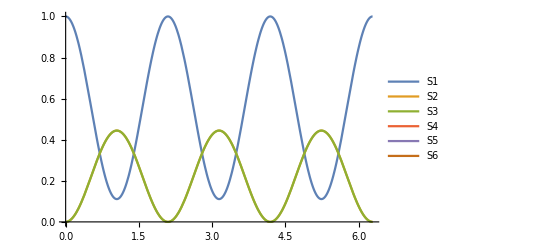

```mathematica
Plot[{wf[t,1],wf[t,2],wf[t,3],wf[t,4],wf[t,5],wf[t,6]},{t,0,2π},PlotLegends->Array["S"<>ToString[#]&,{6}],AxesOrigin->{0,0}]
```

My interpretation: We see that the probability evolves from at t = 0, the spin at x = 1 has 100 % probability of being down. As the state evolves, both spins x = 2 and x = 6 have equal probability of being 1, as this is not a spin wave with momentum, but is is the time-dependent dispersion of the state with the x=1 spin down. As time evolves, x=3 and x=5 states become more probable and then finally, the x=4 spin on the opposing side of the spin chain, becomes the most probable to observe. as up.

### Part 5) Constructing Spin operators

#### In terms of spin operators,

```mathematica
comm[A_,B_]:=A.B-B.A
```

```mathematica
(*spin operator (i = 1,2,3 for x,y,z) acting on the n^th (n ∈ {0, 1, 2, ... , L-1}) spin on the chain*)
Subscript[S, n_,i_]:=ℏ/2 Subscript[σ, n,i]
ℏ=1;
```

```mathematica
(*periodicity in the pauli index i*)
Subscript[S, n,4]==Subscript[S, n,1]
```

True

#### Constructing S^z

Does S^z commute with H?

```mathematica
Sz[L_?IntegerQ] := S[L]=Sum[Subscript[S, i,3],{i,1,L}];
```

```mathematica
Table[Module[{},L=n;comm[H[L],Sz[L]]]==Array[0&,{2^n,2^n}],{n,2,8}]
```

{True,True,True,True,True,True,True}

```mathematica
L=2;
Sz[L]
```

{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}}

What are the eigenvalues?

```mathematica
L=4;
```

```mathematica
eigenEqSz[pos_]:= Sz[L].Subscript[Length@pos,pos, L]==mz ℏ Subscript[Length@pos,pos, L]
```

```mathematica
testPos = {{},{0},{0,1},{0,1,2},{0,1,2,3}};
```

```mathematica
Quiet@Table[Print["Down spins at: "<>ToString@testPos[[i]]<>", mz = "<>ToString[mz/.Solve[eigenEqSz[testPos[[i]]],mz][[1]]]],{i,1, Length@testPos}];
```

Down spins at: {}, mz = 2

Down spins at: {0}, mz = 2

Down spins at: {0, 1}, mz = 1

Down spins at: {0, 1, 2}, mz = 0

Down spins at: {0, 1, 2, 3}, mz = -1

The spectrum of S^z seems correct . Now instead of using the handmade states, we should be able to get these by the spin flip operators:

#### Spin flip operators

```mathematica
Subscript[flipS, n_,sign_]:=<|up->(Subscript[S, n,1]+ⅈ Subscript[S, n,2]),down ->( Subscript[S, n,1]- ⅈ Subscript[S, n,2])|>[[Key[sign]]]
```

```mathematica
L=9;
Table[Subscript[flipS, n, up].Subscript[0, L]==0*Subscript[0, L],{n,1,L}]//FullSimplify
```

{True,True,True,True,True,True,True,True,True}

Lowering operator should flip the n^thsite:

```mathematica
L=6;
Table[{n,Subscript[flipS, n, down].Subscript[0, L]==(ℏ Subscript[1,{n}, L])},{n,1,L}]//TableForm
```

1 | True
2 | True
3 | True
4 | True
5 | True
6 | True

What about the spectrum?

```mathematica
dotWithCount[obj1_,obj2_]:=Module[{},
dotcount++;
Dot[obj1,obj2]
]
```

```mathematica
L=4;
```

```mathematica
eigenEqSz[n_]:= Module[{},
dotcount= 0;
out=((Sz[L]-mz ℏ*IdentityMatrix[Dimensions@Sz[L]]).Nest[dotWithCount[Subscript[flipS, dotcount+1, down],#]&,Subscript[0, L],n]== 0);
dotcount=0;
out]
```

```mathematica
testPos = {{},{0},{0,1},{0,1,2},{0,1,2,3}};
```

```mathematica
Quiet@Table[Print["Down spins at: "<>ToString@testPos[[i]]<>", mz = "<>ToString[mz/.Solve[eigenEqSz[Length@testPos[[i]]],mz][[1]]]],{i,1, Length@testPos}];
```

Down spins at: {}, mz = 2

Down spins at: {0}, mz = 1

Down spins at: {0, 1}, mz = 0

Down spins at: {0, 1, 2}, mz = -1

Down spins at: {0, 1, 2, 3}, mz = -2

So the spectrum is identical, with states being different .

```mathematica
L=4;
flipSAll[L_?IntegerQ]:=Sum[Subscript[flipS, n, down],{n,1,L}]
```

```mathematica
measureSz[ket_]:=Module[{L,sol,zcomp,mz},
L = Log[2, Length@ket];
sol = Flatten@Solve[(Sz[L]-mz ℏ*IdentityMatrix[Dimensions@Sz[L]]).ket==0,mz];
If[Length@sol<1,
Print["Not an eigenstate of S_z."];,
zcomp = mz/.sol;
Print["m_z is "<>ToString@zcomp];
zcomp
]
]
```

```mathematica
measureSz[Nest[Dot[flipSAll[L],#]&,Subscript[0, L],L/2]]
```

m_z is 0

0

#### Constructing total spin operator S^2

```mathematica
(*spin vector for the nth spin operators*)
 Subscript[S̄, n_]:= Table[Subscript[S, n,i],{i,1,3}]
```

Then the total spin vector is (∑_(n=1)^L (S̄)_n)^2= ((S̄)_1)^2+....
We need the usual ((S̄)_i)^2, which we know, and cross terms of the form a((S̄)_i·(S̄)_j).
Just by distributing the multiplication over the sum,

```mathematica
totalS[L_]:=totalS[L]=Module[{j,k,l,cross,fakeS,realS},
(*First, create empty vector objects,placeholders for Subscript[S̄, n]*)
fakeS = Table[Array[Subscript[s, i,#]&,{3}],{i,1,L}];
realS=Table[ Subscript[S̄, i],{i,1,L}];
fakeS=realS;
cross={};
For[j=1,j<=Length@fakeS,j++,For[l=1,l<=Length@fakeS,l++,AppendTo[cross,vecMatDot[fakeS[[l]],fakeS[[j]]]]]];
Total@cross
]
```

```mathematica
Total@{Array[Subscript[a, ##]&,{2,2}],Array[Subscript[b, ##]&,{2,2}]}
```

{{a_(1,1)+b_(1,1),a_(1,2)+b_(1,2)},{a_(2,1)+b_(2,1),a_(2,2)+b_(2,2)}}

Test the s = 1 case (2 spins) :

```mathematica
measureS2[ket_]:= Module[{L,s2,ssplus1,A,sols, ssquared,sol},
L = Log[2, Length@ket];
sol = Flatten@Quiet@Solve[(totalS[L]-A*IdentityMatrix[2^L]).ket==0,A];
ssplus1 = Quiet@(A/.sol[[1]]);
If[Length@sol<1,
Print["Not an eigenstate of S^2."],
ssquared = Max@(s2/.Solve[s2(s2+1)==ssplus1/ℏ^2,s2]);
Print["S^2 value is "<>ToString@ssquared];
ssquared
]
]
```

```mathematica
L=2;
totalS[L]
```

{{2,0,0,0},{0,1,1,0},{0,1,1,0},{0,0,0,2}}

```mathematica
L=5;
measureS2[Subscript[0, L]]
measureS2[Nest[Dot[flipSAll[L],#]&,Subscript[0, L],2]]
```

S^2 value is 5
-
2

5/2

S^2 value is 5
-
2

5/2

As expected. Testing this for the other triplet configurations:

### Part 6) n - particle Bethe states Ket[M]

The syntax is as follows :
ψ[p] is the state, with p being the list of momenta:
the default form is assumed to be as {k_1,k_2, ... , k_i}

```mathematica
Subscript[ψ[p_?ArrayQ], L_]:=Module[{M,range,xx,Mstate},
(*M = total magnetization, # of down spins*)
M = Length@p;
xx = Join[{0},Array[Subscript[x, #]&,{M}]];
Mstate = Sum[f[p] Subscript[M,xx[[2;;M+1]], L],Evaluate[Sequence@@Table[{xx[[k]],xx[[k-1]]+1,L},{k,2,M+1}]]];
Mstate
]
```

```mathematica
xx = Join[{0},Array[Subscript[x, #]&,{2}]];
```

```mathematica
Evaluate[Sequence@@Table[{xx[[k]],xx[[k-1]]+1,L},{k,2,2+1}]]
```

Sequence[{x_1,1,5},{x_2,1+x_1,5}]

```mathematica
f[pos_?ArrayQ]:= Module[{M,indices,tab,poses,out},
M=Length@pos;
indices =Tuples[Table[i,{i,1,M}],M];
tab =Tuples[Table[Subscript[k, i],{i,1,M}],M];
poses= Tuples[Table[Subscript[x, i],{i,1,M}],M];
out={};
For[i=1, i<=Length@tab,i++,
If[!DuplicateFreeQ[tab[[i]]],

tab=Delete[tab,i];
indices=Delete[indices,i];
poses = Delete[poses,i];
i--,

AppendTo[out,Signature@indices[[i]]*A[tab[[i]]]*Exp[ⅈ*Plus@@(tab[[i]]*Table[poses[[1]],{k,1,Length@poses}][[i]])]]
]
];
Total@(out/.Thread[DeleteDuplicates@Flatten@tab->pos])
]
```

```mathematica
Thread[{a,b,c}->{x,y,z}]
```

{a→x,b→y,c→z}

```mathematica
Clear@s
```

```mathematica
f[{k1,k2,k3}]
```

ⅇ^(ⅈ (k1 x_1+k2 x_2+k3 x_3)) A[{k1,k2,k3}]-ⅇ^(ⅈ (k1 x_1+k3 x_2+k2 x_3)) A[{k1,k3,k2}]-ⅇ^(ⅈ (k2 x_1+k1 x_2+k3 x_3)) A[{k2,k1,k3}]+ⅇ^(ⅈ (k2 x_1+k3 x_2+k1 x_3)) A[{k2,k3,k1}]+ⅇ^(ⅈ (k3 x_1+k1 x_2+k2 x_3)) A[{k3,k1,k2}]-ⅇ^(ⅈ (k3 x_1+k2 x_2+k1 x_3)) A[{k3,k2,k1}]

```mathematica
ff[m_]:=Module[{MyPerm=Permutations[Range[1,m]]},Sum[Signature[MyPerm[[l]]]A[MyPerm[[l]]]phase[MyPerm[[l]]],{l,1,m!}]]
```

```mathematica
ff[3]
```

ⅇ^(ⅈ (k[1] x[1]+k[2] x[2]+k[3] x[3])) A[{1,2,3}]-ⅇ^(ⅈ (k[1] x[1]+k[3] x[2]+k[2] x[3])) A[{1,3,2}]-ⅇ^(ⅈ (k[2] x[1]+k[1] x[2]+k[3] x[3])) A[{2,1,3}]+ⅇ^(ⅈ (k[2] x[1]+k[3] x[2]+k[1] x[3])) A[{2,3,1}]+ⅇ^(ⅈ (k[3] x[1]+k[1] x[2]+k[2] x[3])) A[{3,1,2}]-ⅇ^(ⅈ (k[3] x[1]+k[2] x[2]+k[1] x[3])) A[{3,2,1}]

```mathematica
phase[myperm_]:=Module[{m=Length[myperm],myk=Thread[k[myperm]]},Exp[ⅈ Sum[myk[[j]]*x[j],{j,1,m}]]];
```

```mathematica
Clear@A;A[pos_?ArrayQ]:=Product[s[pos[[l]],pos[[j]]],{l,1,Length@pos},{j,1,l-1}]
```

```mathematica
Subscript[ψ[{k1,k2}], L]
```

{0,0,0,-ⅇ^(ⅈ (5 k1+4 k2)) s[k1,k2]+ⅇ^(ⅈ (4 k1+5 k2)) s[k2,k1],0,-ⅇ^(ⅈ (5 k1+3 k2)) s[k1,k2]+ⅇ^(ⅈ (3 k1+5 k2)) s[k2,k1],-ⅇ^(ⅈ (4 k1+3 k2)) s[k1,k2]+ⅇ^(ⅈ (3 k1+4 k2)) s[k2,k1],0,0,-ⅇ^(ⅈ (5 k1+2 k2)) s[k1,k2]+ⅇ^(ⅈ (2 k1+5 k2)) s[k2,k1],-ⅇ^(ⅈ (4 k1+2 k2)) s[k1,k2]+ⅇ^(ⅈ (2 k1+4 k2)) s[k2,k1],0,-ⅇ^(ⅈ (3 k1+2 k2)) s[k1,k2]+ⅇ^(ⅈ (2 k1+3 k2)) s[k2,k1],0,0,0,0,-ⅇ^(ⅈ (5 k1+k2)) s[k1,k2]+ⅇ^(ⅈ (k1+5 k2)) s[k2,k1],-ⅇ^(ⅈ (4 k1+k2)) s[k1,k2]+ⅇ^(ⅈ (k1+4 k2)) s[k2,k1],0,-ⅇ^(ⅈ (3 k1+k2)) s[k1,k2]+ⅇ^(ⅈ (k1+3 k2)) s[k2,k1],0,0,0,-ⅇ^(ⅈ (2 k1+k2)) s[k1,k2]+ⅇ^(ⅈ (k1+2 k2)) s[k2,k1],0,0,0,0,0,0,0}

```mathematica
L=4;
Subscript[ψ[{π,(3π)/2}], L]
measureSz@Subscript[ψ[{π,(3π)/2}], L]
measureS2@Subscript[ψ[{π,(3π)/2}], L]
```

{0,0,0,-ⅈ s[π,(3 π)/2]-s[(3 π)/2,π],0,s[π,(3 π)/2]+s[(3 π)/2,π],-s[π,(3 π)/2]+ⅈ s[(3 π)/2,π],0,0,ⅈ s[π,(3 π)/2]-s[(3 π)/2,π],-ⅈ s[π,(3 π)/2]-ⅈ s[(3 π)/2,π],0,ⅈ s[π,(3 π)/2]+s[(3 π)/2,π],0,0,0}

m_z is 0

0

Not an eigenstate of S^2.

### Part 7) Constraining the momenta of n-particle Bethe eigenstates

#### Definitions :

```mathematica
Clear[L,M];
```

```mathematica
u[k_]:= 1/2 Cot[k/2]
```

```mathematica
Subscript[e, n_][u_]:=(u+(ⅈ n)/2)/(u - (ⅈ n)/2)
```

```mathematica
s[kl_,kj_]:=ⅈ(Subscript[e, 1][u[kj]]−1) (Subscript[e, 1][u[kl]]−1) (u[kl]−u[kj]−ⅈ)
```

```mathematica
s[1,2]//FullSimplify
```

1-2 ⅇ^(2 ⅈ)+ⅇ^(3 ⅈ)

The eigenvalues of Bethe states should be

```mathematica
EE[pos_?ArrayQ]:= Sum[ϵ[pos[[i]]], {i,1,Length@pos}]
```

```mathematica
S[k0_,k1_]:= (u[k1]-u[k0]-ⅈ)/(u[k1]-u[k0]+ⅈ);
```

with the quantization condition

```mathematica
quantizationExp = Exp[ⅈ Subscript[k, j] L]== Product[S[Subscript[k, l],Subscript[k, j]], {l,1,M}]/S[Subscript[k, j],Subscript[k, j]]
```

ⅇ^(ⅈ L k_j)==-∏_(l=1)^M (-ⅈ+1/2 Cot[k_j/2]-1/2 Cot[k_l/2])/(ⅈ+1/2 Cot[k_j/2]-1/2 Cot[k_l/2])

As a function of u_j:

```mathematica
quantizationU =Subscript[e, 1][Subscript[u, j]]== Product[Subscript[e, 2][Subscript[u, j]-Subscript[u, l]], {l,1,M}]/(Subscript[e, 2][Subscript[u, j]-Subscript[u, j]])
```

(ⅈ/2+u_j)/(-ⅈ/2+u_j)==-∏_(l=1)^M (ⅈ+u_j-u_l)/(-ⅈ+u_j-u_l)

```mathematica
$Assumptions = {u ∈Reals,n∈Integers};
```

Remark: j ranges from 1 to M.

```mathematica
ⅈ Log[Subscript[e, n][u]]+π==2 ArcTan[2 u/n]//FullSimplify
```

π+ⅈ Log[1-(2 n)/(n+2 ⅈ u)]==2 ArcTan[(2 u)/n]

```mathematica
betheEqs = Hold@((Subscript[e, 1][Subscript[u, j]])^L==Product[Subscript[e, 2][Subscript[u, j]-Subscript[u, l]],{l,0,M-1}]/(Subscript[e, 2][Subscript[u, j]-Subscript[u, j]]))
```

Hold[e_1[u_j]^L==(∏_(l=0)^(M-1) e_2[u_j-u_l])/e_2[u_j-u_j]]

```mathematica
Subscript[q, n_][u_]:=2ArcTan[2 u/n](*ⅈ Log[Subscript[e, n][u]]+π*)
```

```mathematica
Subscript[q, 2][Subscript[u, j]-Subscript[u, j]]
```

0

```mathematica
logBethe=Hold@(L Subscript[q, 1][Subscript[u, j]] == Sum[Subscript[q, 2][Subscript[u, j]-Subscript[u, l]],{l,0,M-1}]-Subscript[q, 2][Subscript[u, j]-Subscript[u, j]]+2π Subscript[J, j])
```

Hold[L q_1[u_j]==∑_(l=0)^(M-1) q_2[u_j-u_l]-q_2[u_j-u_j]+2 π J_j]

The counting function

```mathematica
zz[u_, uu_?ArrayQ]:=L Subscript[q, 1][u] - Sum[Subscript[q, 2][u-uu[[l]]],{l,1,Length@uu}]-Subscript[q, 2][u-u]
(*Provide uu as a table Table[u[Subscript[k, l]],{l,1,M-1}], so that all the momenta but u = Subscript[k, j] are in the list.*)
```

Dropping the sum, in ( L q_1[u_j]==∑_(l=0)^(M-1) q_2[u_j-u_l]-q_2[u_j-u_j]+2 π J_j), we get

```mathematica
Solve[L Subscript[q, 1][Subscript[u, j]]==2 π Subscript[J, j], Subscript[u, j]]//FullSimplify
```

{{u_j→ConditionalExpression[1/2 Tan[(π J_j)/L], ]}}

#### Exercise 1) L=4, M =2. Find the Bethe roots numerically and show that it is an eigenstate.

```mathematica
getK[uu_?ArrayQ]:= Table[π*Rationalize@N@((k/.FindRoot[u[k]==uu[[i]],{k,π+RandomReal[{-1,1}]}])/π),{i,1,Length@uu}]
```

```mathematica
betheSolve[LL_,MM_,steps_]:=Module[{Jvalues, Js,Jreplace,uvals,jEq},
L=LL;
M=MM;
If[M>L/2,
M=L-M;Print["This state is equivalent to M = "<>ToString[M] <>" state. Correcting M to equivalent value."],""
];
Print["The J_is are half-integers: "<> ToString@EvenQ@(L-M)];
Subscript[J, max] = 1/2(L-M-1);
Print["Values of J_i:" <>ToString@Table[i//N,{i,-Subscript[J, max],Subscript[J, max],1}]];
Jvalues = Table[i,{i,-Subscript[J, max],Subscript[J, max],1}];
Js = Transpose@Table[{j,Subscript[J, j]},{j,1,Subscript[J, max]*2+1,1}];
Jreplace= Thread[Js[[2]]->Jvalues];
uvals = {{},{}};
For[p=1,p<=M,p++,
AppendTo[uvals[[2]],Subscript[u, p,1]/.(With[{i=1,j=p},Solve[zz[Subscript[u, j,i],uvals[[1]]]==2π Subscript[J, j],Subscript[u, j,i]]]//FullSimplify//Normal)/.Jreplace//N]
];
For[i=2, i<=steps,i++,
AppendTo[uvals,{}];
For[j=1,j<=M,j++,
jEq = zz[Subscript[u, j,i],uvals[[i]]]==2 π Subscript[J, j];
AppendTo[uvals[[i+1]], Subscript[u, j,i]/.Quiet@FindRoot[jEq/.Jreplace,{Subscript[u, j,i],Abs@uvals[[i,j]]},MaxIterations->1000]];
]
];
Print["Allowed momenta:"];
Print@getK@Last@uvals;
getK@Last@uvals
]
```

```mathematica
momenta = betheSolve[4,2,50];
```

The J_is are half-integers: True

Values of J_i:{-0.5, 0.5}

Allowed momenta:

{(4 π)/3,(2 π)/3}

```mathematica
L=4;
Subscript[ψ[momenta], L]//N;
measureSz@Subscript[ψ[momenta], L]
measureS2@Chop@Subscript[ψ[momenta], L]
```

m_z is 0

0

S^2 value is 0

0

```mathematica
H[L].Subscript[ψ[momenta], L]==EE[momenta] Subscript[ψ[momenta], L]//FullSimplify
```

True

#### Exercise 2) L = 6, M = 3. Find the Bethe roots numerically and show that it is an eigenstate .

```mathematica
momenta = betheSolve[6,3,50];
```

The J_is are half-integers: False

Values of J_i:{-1., 0., 1.}

Allowed momenta:

{4.56042,π,1.72277}

```mathematica
L=6;
measureSz@Subscript[ψ[momenta], L]
measureS2@(Chop@Subscript[ψ[momenta], L])
```

m_z is 0

0

Not an eigenstate of S^2.

```mathematica
Chop[totalS[L].Subscript[ψ[momenta], L]]==0 Subscript[0, L]//Chop
```

True

```mathematica
Max@(s/.Solve[s*(s+1)==0,s])
```

0

total spin is 0.

```mathematica
H[L].Subscript[ψ[momenta], L]==EE[momenta] Subscript[ψ[momenta], L]
```

False

```mathematica
H[L].Subscript[ψ[momenta], L]
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.39266×10^-12-190.732 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-4.96669×10^-12+629.943 ⅈ,0.+0. ⅈ,3.38574×10^-12-629.943 ⅈ,-1.10845×10^-12+190.732 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4.35918×10^-12-629.943 ⅈ,0.+0. ⅈ,-8.3844×10^-12+1450.62 ⅈ,3.74101×10^-12-629.943 ⅈ,0.+0. ⅈ,0.+0. ⅈ,2.61835×10^-12-629.943 ⅈ,-2.24532×10^-12+629.943 ⅈ,0.+0. ⅈ,5.82645×10^-13-190.732 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.13332×10^-12+190.732 ⅈ,0.+0. ⅈ,4.20997×10^-12-629.943 ⅈ,-3.8618×10^-12+629.943 ⅈ,0.+0. ⅈ,0.+0. ⅈ,-3.10507×10^-12+629.943 ⅈ,7.23333×10^-12-1450.62 ⅈ,0.+0. ⅈ,-2.95941×10^-12+629.943 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,7.4607×10^-13-190.732 ⅈ,-2.90612×10^-12+629.943 ⅈ,0.+0. ⅈ,3.12284×10^-12-629.943 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-7.21201×10^-13+190.732 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Chop[H[L].Subscript[ψ[momenta], L]]==Chop[EE[momenta] Subscript[ψ[momenta], L]]
```

True

```mathematica
Chop[H[L].Subscript[ψ[momenta], L]]
```

{0,0,0,0,0,0,0,0.-190.732 ⅈ,0,0,0,0.+629.943 ⅈ,0,0.-629.943 ⅈ,0.+190.732 ⅈ,0,0,0,0,0.-629.943 ⅈ,0,0.+1450.62 ⅈ,0.-629.943 ⅈ,0,0,0.-629.943 ⅈ,0.+629.943 ⅈ,0,0.-190.732 ⅈ,0,0,0,0,0,0,0.+190.732 ⅈ,0,0.-629.943 ⅈ,0.+629.943 ⅈ,0,0,0.+629.943 ⅈ,0.-1450.62 ⅈ,0,0.+629.943 ⅈ,0,0,0,0,0.-190.732 ⅈ,0.+629.943 ⅈ,0,0.-629.943 ⅈ,0,0,0,0.+190.732 ⅈ,0,0,0,0,0,0,0}

```mathematica
Timing@betheSolve[100,10,50]
```

The J_is are half-integers: True

Values of J_i:{-44.5, -43.5, -42.5, -41.5, -40.5, -39.5, -38.5, -37.5, -36.5, -35.5, -34.5, -33.5, -32.5, -31.5, -30.5, -29.5, -28.5, -27.5, -26.5, -25.5, -24.5, -23.5, -22.5, -21.5, -20.5, -19.5, -18.5, -17.5, -16.5, -15.5, -14.5, -13.5, -12.5, -11.5, -10.5, -9.5, -8.5, -7.5, -6.5, -5.5, -4.5, -3.5, -2.5, -1.5, -0.5, 0.5, 1.5, 2.5, 3.5, 4.5, 5.5, 6.5, 7.5, 8.5, 9.5, 10.5, 11.5, 12.5, 13.5, 14.5, 15.5, 16.5, 17.5, 18.5, 19.5, 20.5, 21.5, 22.5, 23.5, 24.5, 25.5, 26.5, 27.5, 28.5, 29.5, 30.5, 31.5, 32.5, 33.5, 34.5, 35.5, 36.5, 37.5, 38.5, 39.5, 40.5, 41.5, 42.5, 43.5, 44.5}

Allowed momenta:

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{3.40816,3.39332,3.3193,2.71962,5.55768,2.55793,5.4087,5.33681,5.26629,5.19688}

{1.78125,{2.66513,3.01288,3.96973,3.67449,5.55768,3.65072,5.4087,5.33681,5.26629,5.19688}}

### Part 8) Dicke States

#### Dicke Circuit:

```mathematica
1/(√6)(Subscript[2,{1,2}, 4]+Subscript[2,{1,3}, 4]+Subscript[2,{1,4}, 4]+Subscript[2,{2,3}, 4]+Subscript[2,{2,4}, 4]+Subscript[2,{3,4}, 4])-{0.,0.,0.,0.40824829,0.,0.40824829,0.40824829,0.,0.,0.40824829,0.40824829,0.,0.40824829,0.,0.,0.}
```

{0.,0.,0.,4.63863×10^-10,0.,4.63863×10^-10,4.63863×10^-10,0.,0.,4.63863×10^-10,4.63863×10^-10,0.,4.63863×10^-10,0.,0.,0.}

```mathematica
{0.+0.j,0.+0.j,0.+0.j,0.40824829+0.j,0.+0.j,0.40824829+0.j,0.40824829+0.j,0.+0.j,0.+0.j,0.40824829+0.j,0.40824829+0.j,0.+0.j,0.40824829+0.j,0.+0.j,0.+0.j,-0.+0.j}
```

{0.,0.,0.,0.408248,0.,0.408248,0.408248,0.,0.,0.408248,0.408248,0.,0.408248,0.,0.,0.}

```mathematica
k[0]=1;
k[1]=2
```

2

```mathematica
{0,0,0,ⅇ^(ⅈ (2 k[0]+3 k[1])) (1-2 ⅇ^(ⅈ k[0])+ⅇ^(ⅈ (k[0]+k[1])))-ⅇ^(ⅈ (3 k[0]+2 k[1])) (1-2 ⅇ^(ⅈ k[1])+ⅇ^(ⅈ (k[0]+k[1]))),0,ⅇ^(ⅈ (k[0]+3 k[1])) (1-2 ⅇ^(ⅈ k[0])+ⅇ^(ⅈ (k[0]+k[1])))-ⅇ^(ⅈ (3 k[0]+k[1])) (1-2 ⅇ^(ⅈ k[1])+ⅇ^(ⅈ (k[0]+k[1]))),ⅇ^(ⅈ (k[0]+2 k[1])) (1-2 ⅇ^(ⅈ k[0])+ⅇ^(ⅈ (k[0]+k[1])))-ⅇ^(ⅈ (2 k[0]+k[1])) (1-2 ⅇ^(ⅈ k[1])+ⅇ^(ⅈ (k[0]+k[1]))),0,0,ⅇ^(3 ⅈ k[1]) (1-2 ⅇ^(ⅈ k[0])+ⅇ^(ⅈ (k[0]+k[1])))-ⅇ^(3 ⅈ k[0]) (1-2 ⅇ^(ⅈ k[1])+ⅇ^(ⅈ (k[0]+k[1]))),ⅇ^(2 ⅈ k[1]) (1-2 ⅇ^(ⅈ k[0])+ⅇ^(ⅈ (k[0]+k[1])))-ⅇ^(2 ⅈ k[0]) (1-2 ⅇ^(ⅈ k[1])+ⅇ^(ⅈ (k[0]+k[1]))),0,ⅇ^(ⅈ k[1]) (1-2 ⅇ^(ⅈ k[0])+ⅇ^(ⅈ (k[0]+k[1])))-ⅇ^(ⅈ k[0]) (1-2 ⅇ^(ⅈ k[1])+ⅇ^(ⅈ (k[0]+k[1]))),0,0,0}//N
```

{0.,0.,0.,-0.0559051-0.123597 ⅈ,0.,1.57547-0.582212 ⅈ,0.0379035+0.13025 ⅈ,0.,0.,-0.861618-2.96082 ⅈ,-1.64187+0.354055 ⅈ,0.,-0.0191433-0.134295 ⅈ,0.,0.,0.}

#### Permutation Ancillas :

```mathematica
m3perm = {0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.40824829+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,-0.40824829+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,-0.40824829+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.40824829+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,-0.40824829+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.40824829+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j,0.+0.j};
```

```mathematica
Length@m3perm
```

512

```mathematica
N@(1/(√6))*Flatten@(KroneckerProduct[Subscript[1,{1}, 3],Subscript[1,{2}, 3],Subscript[1,{3}, 3]]+KroneckerProduct[Subscript[1,{2}, 3],Subscript[1,{1}, 3],Subscript[1,{3}, 3]]+KroneckerProduct[Subscript[1,{2}, 3],Subscript[1,{3}, 3],Subscript[1,{1}, 3]]+KroneckerProduct[Subscript[1,{1}, 3],Subscript[1,{3}, 3],Subscript[1,{2}, 3]]+KroneckerProduct[Subscript[1,{3}, 3],Subscript[1,{1}, 3],Subscript[1,{2}, 3]]+KroneckerProduct[Subscript[1,{3}, 3],Subscript[1,{2}, 3],Subscript[1,{1}, 3]])-m3perm
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.63863×10^-10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.816497,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.816497,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.63863×10^-10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.816497,0.,0.,0.,0.,0.,0.,4.63863×10^-10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}